```mathematica
m=3.0;
λ=0.3;
Δ=0.0;
R=0.0;
HAM=({{m-(Cos[kx]+Cos[ky]), λ*(Sin[kx]-ⅈ*Sin[ky]), R*ⅈ*(Sin[kx]-ⅈ*Sin[ky]), -Δ}, {λ*(Sin[kx]+ⅈ*Sin[ky]), -m+(Cos[kx]+Cos[ky]), Δ, 0}, {-R*ⅈ*(Sin[kx]+ⅈ*Sin[ky]), Δ, m-(Cos[kx]+Cos[ky]), λ*(-Sin[kx]-ⅈ*Sin[ky])}, {-Δ, 0, λ*(-Sin[kx]+ⅈ*Sin[ky]), -m+(Cos[kx]+Cos[ky])}});
HAM2=HAM.HAM;
HAM3=HAM.HAM.HAM;
HAM4=HAM.HAM.HAM.HAM;
μ=-0.2;
om=({{μ+ⅈ*0.5, 0, 0, 0}, {0, μ+ⅈ*0.5, 0, 0}, {0, 0, μ+ⅈ*0.5, 0}, {0, 0, 0, μ+ⅈ*0.5}});
(*invHAM=Inverse[om-HAM]//FullSimplify*)
(*invHAM.HAM//FullSimplify//MatrixForm*)
```

```mathematica
Nkx=20.;
Nky=20.;
Nkz=1.;
Nkx*Nky*Nkz
```

400.

```mathematica
ConstructDMFTHam[Mat_,Nkx_,Nky_,Nkz_,DirPath_]:=Module[{Ham={},i,j,k,l,kxx,kyy,kzz,streaM},
For[i=0,i<Nkx,kxx=-π+2 π*i/Nkx;
For[j=0,j<Nky,kyy=-π+2 π*j/Nky;
For[k=0,k<Nkz,kzz=-π+2 π*k/Nkz;
Ham=Append[Ham,{N[kxx],N[kyy],N[kzz]}];
For[l=1,l≤Dimensions[Mat][[1]],Ham=Append[Ham,Flatten[Chop[Riffle[Re[Mat[[l]]],Im[Mat[[l]]]]]]/.{kx->kxx,ky->kyy,kz->kzz}];
l++];
k++];
j++];
i++];
streaM=OpenWrite[DirPath<>"Hkdmft.dat"];
For[i=1,i≤Length[Ham],For[j=1,j≤Length[Ham[[i]]],Chop[Ham[[i,j]]] WriteString[streaM,StringJoin[ToString[NumberForm[Chop[Ham[[i,j]]],{6,6}]]],"  "];
j++];
WriteString[streaM,"\n"];
i++];
Close[streaM];]
```

```mathematica
ConstructDMFTHam[HAM,Nkx,Nky,Nkz,"/home/amaricci/Dropbox/projects_src/NonInteractingModels/TImodels/BHZ4x4_"]
```

### Define Function BandPlot[H,DosPath,BandColor]

This function calculates a band structure, given H, the Hamiltonian, DosPath, the path to folow in q-space and BandColor, a RGB value specifieing the color for each band (basis-function)

```mathematica
(*ClearAll[H,(*DOSPath*),BandColor]*)
BandPlot[H_,DOSPath_,BandColor_]:=Module[{values,colors,pointsize,functions,RBandColor,Jtot,GBandColor,BBandColor,temp,i,j,k,Jlist,MinVals,MaxVals},
values={};
colors={};
pointsize={};
functions={};
Jlist={0};
MinVals={};
MaxVals={};
RBandColor=BandColor[[All,1]];
GBandColor=BandColor[[All,2]];
BBandColor=BandColor[[All,3]];
temp=0;
Jtot=0;
 For[i=1,i<Length[DOSPath],
jmax=((DOSPath[[i+1]]-DOSPath[[i]]).(DOSPath[[i+1]]-DOSPath[[i]]))^0.5 200;
Jtot=Jtot+jmax;
Jlist=Append[Jlist,Jtot];
For[j=1,j≤jmax,
kx=DOSPath[[i,1]]+j/jmax(DOSPath[[i+1,1]]-DOSPath[[i,1]]);
ky=DOSPath[[i,2]]+j/jmax(DOSPath[[i+1,2]]-DOSPath[[i,2]]);
kz=DOSPath[[i,3]]+j/jmax(DOSPath[[i+1,3]]-DOSPath[[i,3]]);
{Eigenv,eigenfun}=Eigensystem[H]//Chop;
MinVals=Append[MinVals,Min[Eigenv]];
MaxVals=Append[MaxVals,Max[Eigenv]];
For[k=1,k≤Length[H],
values=Append[values,{temp,Eigenv[[k]]}];
colors=Append[colors,{
(eigenfun[[k]]*RBandColor).(Conjugate[eigenfun[[k]]*RBandColor]),(eigenfun[[k]]*GBandColor).(Conjugate[eigenfun[[k]]*GBandColor]),(eigenfun[[k]]*BBandColor).(Conjugate[eigenfun[[k]]*BBandColor])
}];
pointsize=Append[pointsize,0.01];
k++];
temp++;
j++];
i++];
(*i=1;*)

plt=Table[ListPlot[{values[[a]]},PlotRange->{Min[MinVals]-0.05*(Max[MaxVals]-Min[MinVals]),Max[MaxVals]+0.05*(Max[MaxVals]-Min[MinVals])},AspectRatio->1.2,DisplayFunction->Identity,
PlotStyle->{RGBColor[colors[[a]][[1]],colors[[a]][[2]],colors[[a]][[3]]],PointSize[pointsize[[a]]]}],{a,1,Length[values]}];

Picture=Show[{plt,Table[Graphics[Line[{{Jlist[[i]],Min[MinVals]-0.05*(Max[MaxVals]-Min[MinVals])},{Jlist[[i]],Max[MaxVals]+0.05*(Max[MaxVals]-Min[MinVals])}}]],{i,1,Length[Jlist]}]},
FrameTicks->{False,{-14,-12,-10,-8,-6,-4,-2,0,2},False,False},
Frame->True,
FrameLabel->{None,None,None,None},
Axes->True,ImageSize->500,DisplayFunction->$DisplayFunction];
kx=.;
ky=.;
kz=.;
];
```

### Plot Bandstructure

```mathematica
a=1.0;
c=1.0;
```

```mathematica
(*Path through BZ*)
Γ={0,0,0};
Z={π/a,0,0};
F={π/a,π/a,0};
L={((2*π)/(a*3)),0,(π/(3*c))};
DOSPath={Γ,Z,F,Γ};

(*colours*)
R={1,0,0};
Bl={0,0,0};
Rd={0.5,0,0};
G={0,1,0};
Gd={0,0.5,0};
B={0.5,0.5,1};
Cy={0,1,1};
Ge={1,1,0};
Gr={0.5,0.5,0.5};
M={1,0,1};
W={1,1,1};
```

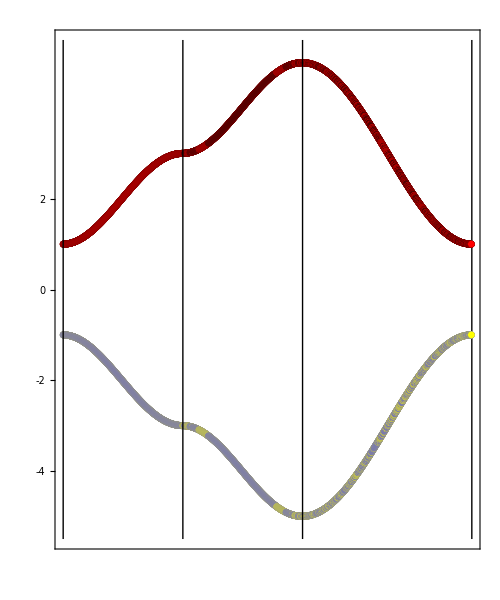

```mathematica
Color={Bl,Ge,R,B};
BandPlot[HAM,DOSPath,Color];
TBP=Picture
```

```mathematica
HAM/.{kx->0,ky->0}//MatrixForm
```

(-1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | -1. | 0
0 | 0 | 0 | 1.)

```mathematica
Ztwo=({{-1., 0, 0, 0}, {0, 1., 0, 0}, {0, 0, -1., 0}, {0, 0, 0, 1.}})+({{0.5, 0, 0, 0}, {0, -0.5, 0, 0}, {0, 0, 0.5, 0}, {0, 0, 0, -0.5}})
```

```mathematica
Eigenvalues[Ztwo]
```

{-0.5,-0.5,0.5,0.5}

```mathematica
Eigensystem[Ztwo]
```

{{-0.5,-0.5,0.5,0.5},{{1.,0.,0.,0.},{0.,0.,1.,0.},{0.,1.,0.,0.},{0.,0.,0.,1.}}}

```mathematica
U=({{1., 0, 0, 0}, {0, -1., 0, 0}, {0, 0, 1., 0}, {0, 0, 0, -1.}});
```

```mathematica
invU=Inverse[U];
```

```mathematica
U.HAM.invU//FullSimplify//MatrixForm
```

```mathematica
HAM/.{kx->π/a,ky->0.0}//MatrixForm
```

(-3. | 3.67394×10^-17+0. ⅈ | 0 | 0
3.67394×10^-17+0. ⅈ | 3. | 0 | 0
0 | 0 | -3. | -3.67394×10^-17+0. ⅈ
0 | 0 | -3.67394×10^-17+0. ⅈ | 3.)

```mathematica
Ztwo=({{-1., 0, 0, 0}, {0, 1., 0, 0}, {0, 0, -1., 0}, {0, 0, 0, 1.}})+({{2.374, 0, 0, 0}, {0, -2.995, 0, 0}, {0, 0, 2.374, 0}, {0, 0, 0, -2.995}})
```

{{1.374,0,0,0},{0,-1.995,0,0},{0,0,1.374,0},{0,0,0,-1.995}}

```mathematica
Eigensystem[Ztwo]
```

{{-1.995,-1.995,1.374,1.374},{{0.,1.,0.,0.},{0.,0.,0.,1.},{1.,0.,0.,0.},{0.,0.,1.,0.}}}